```mathematica
ClearAll["Clobal`*"]
```

# 3 term recurrence

```mathematica
inner[f_,g_,{w_,a_,b_}]:=Integrate[f g w, {x,a,b}](*Assumptions->x ∈ Reals]*)
getCoeff[{fn_,lower_,upper_}]:=Function[{p,r},
Module[{a =inner[p, r,{fn,lower,upper}],b=inner[p,p,{fn,lower,upper}]},
Print["∫",p r fn ," dx = ", a];
Print["||p(||)^2 = ", b ];
a/b]]

getNorm[others_]:=Function[{f},Sqrt[inner[f,f,others]]]
```

```mathematica
coeffPR=getCoeff[{√((1-x)/(1+x)),-1,1}]
norm=getNorm[{√((1-x)/(1+x)),-1,1}]
```

Function[{p$,r$},Module[{a$=inner[p$,r$,{√((1-x)/(1+x)),-1,1}],b$=inner[p$,p$,{√((1-x)/(1+x)),-1,1}]},Print[∫,p$ r$ √((1-x)/(1+x)), dx = ,a$];Print[||p(||)^2 = ,b$];a$/b$]]

Function[{f$},√inner[f$,f$,{√((1-x)/(1+x)),-1,1}]]

```mathematica
w0 = 1
a0 = coeffPR[w0,x w0]
```

1

∫x √((1-x)/(1+x)) dx = -π/2

||p(||)^2 = π

-1/2

```mathematica
w1=2(x w0 - a0 w0)
```

2 (1/2+x)

```mathematica
a1 = coeffPR[w1,x w1]
```

∫4 x (1/2+x)^2 √((1-x)/(1+x)) dx = 0

||p(||)^2 = π

0

```mathematica
c0 = coeffPR[w0, x w1]
```

∫2 x (1/2+x) √((1-x)/(1+x)) dx = π/2

||p(||)^2 = π

1/2

```mathematica
w2=2(x w1- a1 w1 - c0 w0)
```

2 (-1/2+2 x (1/2+x))

```mathematica
Expand[w2]
```

-1+2 x+4 x^2

```mathematica
Expand[p2]
```

-1+(2 x)/3+2 x^2

```mathematica
a2=coeffPR[p2,x p2]
```

<p, r> = -8/2625

||p(||)^2 = 8/75

-1/35

```mathematica
c0=coeffPR[p1, x p2]
```

<p, r> = 8/75

||p(||)^2 = 4/9

6/25

```mathematica
q0=p0/norm[p0]
```

1/(√2)

```mathematica
q1=p1/norm[p1]
```

3/2 (1/3+x)

```mathematica
q2=p2/norm[p2]
```

5/2 √(3/2) (-2/9+1/15 (1/3+x)+x (1/3+x))

```mathematica
Expand[q2]
```

-(√(3/2))/2+√(3/2) x+5/2 √(3/2) x^2

```mathematica
x q1
```

3/2 x (1/3+x)

```mathematica
Expand[3/2 x (1/3+x)]
```

x/2+(3 x^2)/2

```mathematica
-1/15 q1+(√6)/5 q2+√(2/9)q0
```

1/3+1/10 (-1/3-x)+3/2 (-2/9+1/15 (1/3+x)+x (1/3+x))

```mathematica
Expand[1/3+1/10 (-1/3-x)+3/2 (-2/9+1/15 (1/3+x)+x (1/3+x))]
```

x/2+(3 x^2)/2

```mathematica
FullSimplify[Cos[5 ArcCos[x]]]
```

Cos[5 ArcCos[x]]

```mathematica
FunctionExpand[Cos[5 ArcCos[x]]]
```

5 x-20 x^3+16 x^5

General::stop: Further output of FunctionInterpolation::ncvb will be suppressed during this calculation.

InterpolatingFunction[…]

# Reflection Matrix

```mathematica
(* only accept {x,y,z}, this function itself will do the correct convertion *)
reflectionMatrix[x_]:= Module[{v,a},
a=If[Length[Dimensions[x]]==2,x,{x}ᵀ];
v=a/Norm[a]//Simplify;
Print["normalised = ",v//MatrixForm];
Print["v . vᵀ = ", v . vᵀ// Simplify//MatrixForm];
IdentityMatrix[3]-2 (v . vᵀ)//Simplify]
reflectionMatrix[{1,2,3}]
```

normalised = (1/(√14)
√(2/7)
3/(√14))

v . vᵀ = (1/14 | 1/7 | 3/14
1/7 | 2/7 | 3/7
3/14 | 3/7 | 9/14)

{{6/7,-2/7,-3/7},{-2/7,3/7,-6/7},{-3/7,-6/7,-2/7}}

```mathematica
(* which axis ∈ {-1,1} *)
```

```mathematica
houseHoulderReflection[x_,whichAxis_]:=Module[
{y=x},
y[[1]]=y[[1]]-whichAxis*Norm[x];
Print["norm of input", Norm[x]];
Print["reflection against", y];
reflectionMatrix[y]]
Simplify[houseHoulderReflection[{1,2,3},1] . {1,2,3}]
```

norm of input √14

reflection against{1-√14,2,3}

normalised = ((1-√14)/(√(28-2 √14))
√(2/(14-√14))
3/(√(28-2 √14)))

v . vᵀ = (1/2-1/(2 √14) | -1/(√14) | -3/(2 √14)
-1/(√14) | -2/(-14+√14) | -3/(-14+√14)
-3/(2 √14) | -3/(-14+√14) | 9/(28-2 √14))

{√14,0,0}

```mathematica
luDecomposition[mat_]:=Module[{n=Length[mat],a=mat,ls,l,ll,llt},
ls={};
Do[l=IdentityMatrix[n];
Do[l[[k,j]]=-a[[k,j]]/a[[j,j]],{k,j+1,n}];
(* construct l[[i]] --- up *)
Print["l",j,"=",MatrixForm @l];
a=l . a;
(* Subscript[a, i+1]=Subscript[l, i] Subscript[a, i] Subscript[L, 2] Subscript[L, 1] A = Subscript[A, 3] = U *)
Print["mat",j,MatrixForm @ a];
AppendTo[ls,l];
,{j,n-1}];
ll=Fold[#2 . #1 &,IdentityMatrix[n],ls];
(* A=(Subscript[L, 2] Subscript[L, 1])^-1 U *)
ll=Inverse[ll];
Print[MatrixForm[ll]];
{ll,a}
]

luDecomposition[{{1,1,1},{2,4,8},{1,4,9}}]
```

l1=(1 | 0 | 0
-2 | 1 | 0
-1 | 0 | 1)

mat1(1 | 1 | 1
0 | 2 | 6
0 | 3 | 8)

l2=(1 | 0 | 0
0 | 1 | 0
0 | -3/2 | 1)

mat2(1 | 1 | 1
0 | 2 | 6
0 | 0 | -1)

(1 | 0 | 0
2 | 1 | 0
1 | 3/2 | 1)

{{{1,0,0},{2,1,0},{1,3/2,1}},{{1,1,1},{0,2,6},{0,0,-1}}}

```mathematica
{{1,0,0},{2,1,0},{1,3/2,1}}.{{1,1,1},{0,2,6},{0,0,-1}}
```

{{1,1,1},{2,4,8},{1,4,9}}

```mathematica
pluDecomposition[mat_]:=Module[{n=Length[mat],a=mat,ls,l,ll,maxIndex,p},
ls={};
Do[
Print[a[[j;;n,j]]];
maxIndex=Position[a[[j;;n,j]], Max[Map[Abs, a[[j;;n,j]]]]][[1,1]] + j - 1;
Print[maxIndex];
p=permutationMatrix[maxIndex,j,n];
Print[MatrixForm @ p];
a=p.a;
Print["p . a = ", MatrixForm @ a];
AppendTo[ls,p];

l=IdentityMatrix[n];
Do[l[[k,j]]=-a[[k,j]]/a[[j,j]],{k,j+1,n}];
(* construct l[[i]] --- up *)
Print["l",j,"=",MatrixForm @l];
a=l . a;
(* Subscript[a, i+1]=Subscript[l, i] Subscript[a, i] Subscript[L, 2] Subscript[L, 1] A = Subscript[A, 3] = U *)
Print["mat",j,MatrixForm @ a];
AppendTo[ls,l];
,{j,n-1}];
ll=Fold[#2 . #1 &,IdentityMatrix[n],ls];
(* A=(Subscript[L, 2] Subscript[L, 1])^-1 U *)
ll=Inverse[ll];
Print["PL = " MatrixForm[ll]];
Print["checking : ", MatrixForm [ ll . a]];
{ll,a}
]
pluDecomposition[({{0, 2, 1}, {2, 6, 1}, {1, 1, 4}})]
(* this is not correct, I will do it later*)
```

{0,2,1}

2

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1)

p . a = (2 | 6 | 1
0 | 2 | 1
1 | 1 | 4)

l1=(1 | 0 | 0
0 | 1 | 0
-1/2 | 0 | 1)

mat1(2 | 6 | 1
0 | 2 | 1
0 | -2 | 7/2)

{2,-2}

2

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

p . a = (2 | 6 | 1
0 | 2 | 1
0 | -2 | 7/2)

l2=(1 | 0 | 0
0 | 1 | 0
0 | 1 | 1)

mat2(2 | 6 | 1
0 | 2 | 1
0 | 0 | 9/2)

PL =  (0 | 1 | 0
1 | 0 | 0
1/2 | -1 | 1)

checking : (0 | 2 | 1
2 | 6 | 1
1 | 1 | 4)

```mathematica
permutationMatrix[i_,j_,size_]:=If[i==j,IdentityMatrix[size], IdentityMatrix[size][[#]]&/@PermutationList[Cycles[{{i,j}}],size]]
permutationMatrix[1,2,3]
```

{{0,1,0},{1,0,0},{0,0,1}}

```mathematica
Ordering[{3,1,2},-1]
```

{1}

```mathematica
{{1/2,-1/2,1},{1/2,1,0},{1,0,0}}.{{2,4,8},{0,2,5},{0,0,-1/2}}
```

{{1,1,1},{1,4,9},{2,4,8}}

# CholeskyDecomposition

```mathematica
choleskyDecomposition[mat_?SymmetricMatrixQ]:=Module[
{n=Length[mat],mt=mat,v,α,L},
L=ConstantArray[0,{n,n}];
Do[
v=mt[[2;;n-j+1,1]];
Print["v " "=" MatrixForm @ v];
α=mt[[1,1]];
L[[j,j]]=Sqrt[α];
L[[j+1;;n,j]]=v/L[[j,j]];
v={v}ᵀ;
mt=Simplify[mt[[2;;n-j+1,2;;n-j+1]]-(v . vᵀ)/α];
Print["mt =A - (v vᵀ)/a = " MatrixForm @ mt];
,{j,1,n-1}];
L[[n,n]]=Sqrt[mt[[1,1]]];
Print[MatrixForm @ L];
Print [ "checking : "MatrixForm[L . Lᵀ]];
L
]
choleskyDecomposition[({{4, 1, 0}, {1, 4, 1}, {0, 1, 4}})]
```

= v  (1
0)

mt =A - (v vᵀ)/a =  (15/4 | 1
1 | 4)

= v  (1)

mt =A - (v vᵀ)/a =  (56/15)

(2 | 0 | 0
1/2 | (√15)/2 | 0
0 | 2/(√15) | 2 √(14/15))

checking :  (4 | 1 | 0
1 | 4 | 1
0 | 1 | 4)

{{2,0,0},{1/2,(√15)/2,0},{0,2/(√15),2 √(14/15)}}

= v  (-1
0)

mt (3/2 | -1
-1 | 2)

= v  (-1)

mt (4/3)

(√2 | 0 | 0
-1/(√2) | √(3/2) | 0
0 | -√(2/3) | 2/(√3))

{{√2,0,0},{-1/(√2),√(3/2),0},{0,-√(2/3),2/(√3)}}

# Gaussian interpolation

```mathematica
gaussianInterpolation[this_,allPoints_]:=Module[
{others=Select[allPoints, #!=this&]},
Product[(x-i)/(this-i),{i, others}]]
```

```mathematica
guassianFullInterpolation[allPoints_]:=Map[gaussianInterpolation[#,allPoints]&,allPoints]
```

```mathematica
guassianFullInterpolation[{-1/2,1/2}]
```

{1/2-x,1/2+x}

# Interpolation Quadrature

```mathematica
findWeights[pts_,{weight_,lower_,upper_}]:=Module[
{fmls=guassianFullInterpolation[pts],rst},
rst=Map[Integrate[# weight,{x,lower,upper}]&,fmls];
Print @ MatrixForm @ fmls;
Print @ MatrixForm @ Expand @ fmls;
Print @ MatrixForm @   rst;
rst
]
```

```mathematica
findWeights[{-1/(√3),1/(√3)},{1,-1,1}]
```

(-1/2 √3 (-1/(√3)+x)
1/2 √3 (1/(√3)+x))

(1/2-(√3 x)/2
1/2+(√3 x)/2)

(1
1)

{1,1}

(π/8
π/2
-π/8)

(1/6-x/2+x^2/3
4/3-(4 x^2)/3
-1/2+x/2+x^2)

(-1/3 (1-x) (-1/2+x)
-4/3 (-1+x) (1+x)
(-1/2+x) (1+x))

```mathematica
LUDecomposition[{{1,2,-1,0},{2,4,-2,1},{-3,-7,6,1}}]
```

LUDecomposition::sing: Matrix {{1,2,-1,0},{2,4,-2,1},{-3,-7,6,1}} is singular.

{{{1,2,-1,0},{-3,-1,3,1},{2,0,0,1}},{1,3,2},0}

```mathematica
Inverse[{{1, 2}, {3, 4}}]
```

{{-2,1},{3/2,-1/2}}

```mathematica
Grid[{{-2,1},{3/2,-1/2}}]
```

-2 | 1
3/2 | -1/2

# Dual number

```mathematica
With[{x = Dual[a,b]}, {x^10}]
```

{Dual[a^10,10 a^9 b]}

```mathematica
D[Exp[x^2],x]
```

2 ⅇ^(x^2) x

{Dual[ⅇ^(a^2),2 a ⅇ^(a^2)]}

```mathematica
Expand[Sin[θ]^4]
```

Sin[θ]^4

```mathematica
TrigReduce[Sin[θ]^4]
```

1/8 (3-4 Cos[2 θ]+Cos[4 θ])

Sin[θ]^4

# DFT

```mathematica
dFT[fn_,n_]:=FullSimplify/@ ((1/(√n) * FourierMatrix[n]) . Table[fn[(2 Pi x)/n],{x,0,n-1}])
```

```mathematica
dFT[4/(4-Exp[I #])&,3]
```

{64/63,4/63,16/63}

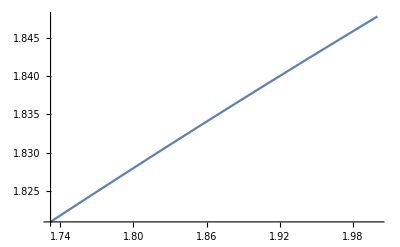

```mathematica
Plot[√(2+√x),{x,√3,2}]
```

```mathematica
Sum[1/4^(3i-1),{i,0,Infinity}]
```

256/63

```mathematica
FourierCoefficient[4/(4-Exp[I θ]),θ,6]
```

1/4096

Csc[ArcCos[x]/2] Sin[(3 ArcCos[x])/2]

```mathematica
Cos[1/2ArcCos[x]]
```

Cos[ArcCos[x]/2]

```mathematica
FunctionExpand[Cos[ArcCos[x]/2]]
```

(√(1+x))/(√2)

```mathematica
DSolve[u'[t]==u[t]+Exp[t]&&u[0]==1,u[t],t]
```

{{u[t]→ⅇ^t (1+t)}}

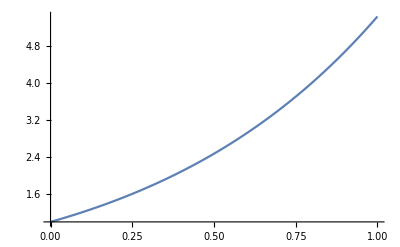

```mathematica
Plot[Exp[t](1+t),{t,0,1}]
```